```mathematica
(*A1*)
n=0;
While[n<100,n= Input["input an integer n≥100"]]
Table[i,{i,n}]
list={};
Do[If[PrimeQ[i],AppendTo[list,i]],{i,n}]
list
sum=0;
Do[sum=sum+list[[i]],{i,Length[list]}]
sum
If[PrimeQ[n],Print["n is prime"],Print["n is not prime. Next prime is ",NextPrime[n]]]
For[list={};i=1,i≤n,i++,If[PerfectNumberQ[i],AppendTo[list,i]]]
list
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103}

1264

n is not prime. Next prime is 107

{6,28}

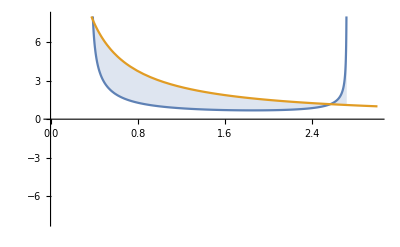

```mathematica
(*A2*)
Plot[{1/(x √(1-(Log[x])^2)),3/x},{x,0,3},Filling->{1->{2}},PlotRange->8]
Clear[x,y]

(*∫_-3^3 ∫_(-√(9-x^2))^(√(9-x^2)) ∫_-3^(3-x) (x^2+y^2-9)ⅆzⅆyⅆx*)
(*∫_-3^3 ∫_(-√(9-y^2))^(√(9-y^2)) ∫_(-√(9-x^2-y^2))^(√(9-x^2-y^2)) √(x^2+y^2+z^2)ⅆzⅆxⅆy*)
```

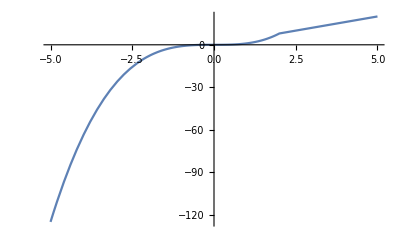

Limit[f[x],x→2]

FindRoot::jsing: Encountered a singular Jacobian at the point {c} = {0.}. Try perturbing the initial point(s).

{c→0.}

```mathematica
(*B1*)
Clear[f,x,y,c]
f[x_]:=x^3/;x<2;
f[x_]:=4 x/;x≥2;
Plot[f[x],{x,-5,5}]
Limit[f[x],x->2]
Clear[f]
f[x_]=x^3;
FindRoot[f'[c]==(f[2]-f[0])/(2-0),{c,0}]
```

```mathematica
(*B2*)
Clear[A,b]
A=({{1, 1, 2}, {2, 4, -3}, {3, 6, -5}});
b={{9},{1},{0}};
Det[A]
If[Det[A]≠0,Print["A is invertible, Inverse of A = ",MatrixForm[Inverse[A]]],Print["A is not invertible"]]
Inverse[A].b
DiagonalizableMatrixQ[A]
```

-1

A is invertible, Inverse of A = (2 | -17 | 11
-1 | 11 | -7
0 | 3 | -2)

{{1},{2},{3}}

True